# Beam Fitting Last Updated: 02/17/2022

```mathematica
Quit[];
```

```mathematica
(*Remove["Global`*"];ClearInOut[];*)
```

## Prep

## Plotting Setup

```mathematica
SetOptions[Plot,ImageSize->Large,PlotRange->Full];
SetOptions[ListPlot,ImageSize->Large,PlotRange->Full];
```

```mathematica
Off[General::munfl];
```

## Global Variables

```mathematica
inch=2.54*^-2;
cm=1*^-2;mm=1*^-3;um=1*^-6;nm=1*^-9;
```

```mathematica
pixelWidth=4.4*^-6;(*length per pixel for pixelink camera*)
```

## Image Import

```mathematica
(*set directory and filetype*)
SetDirectory["/Users/claytonho/Documents/Research/Mathematica/Beams/Data/Feb16_866"];
ParallelEvaluate[SetDirectory["/Users/claytonho/Documents/Research/Mathematica/Beams/Data/Feb16_866"]];
imgNames=FileNames["*bmp*"]
```

{12 inch 866nm.bmp,15 inch 866nm.bmp,18 inch 866nm.bmp,21 inch 866nm.bmp,24 inch 866nm.bmp,36 inch 866nm.bmp,3 inch 866nm.bmp,6 inch 866nm.bmp,9 inch 866nm.bmp}

```mathematica
λ0=854*nm;(*wavelength*)
waistDist={12,15,18,21,24,36,3,6,9}*inch;(*beam waist measurement distances*)
```

## Get Images

```mathematica
AbsoluteTiming[
imdRaw=ParallelMap[Import,imgNames];
imdRaw=ColorConvert[#,"Grayscale"]&/@imdRaw;(*for bmp only*)
imdRaw=ImageData/@imdRaw;
]
```

{2.48199,Null}

```mathematica
(*number of images*)
numImages=Length[imgNames];
(*image dimensions*)
imgDim=Dimensions[imdRaw[[1]]]//Reverse;
```

```mathematica
(*order images by measurement distance*)
distOrder=Ordering[waistDist];
waistDist=Sort[waistDist];
imdRaw=imdRaw[[distOrder]];
```

## Check Saturation/Clipping

{9,1200}

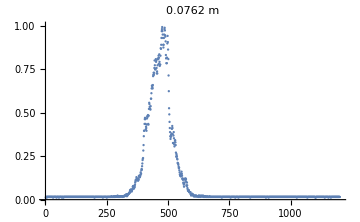
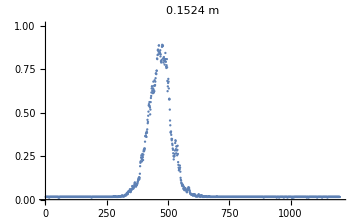
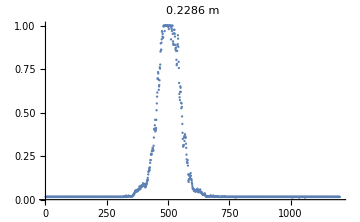
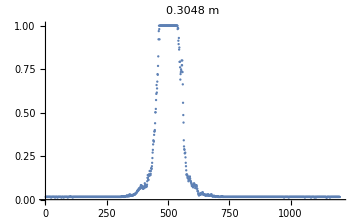
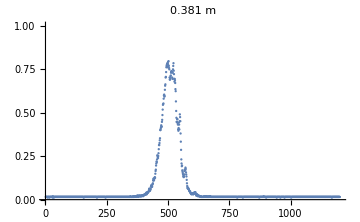
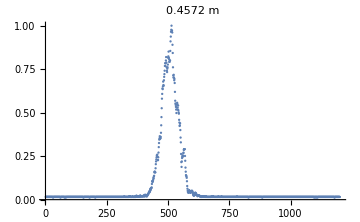
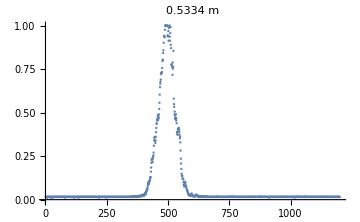
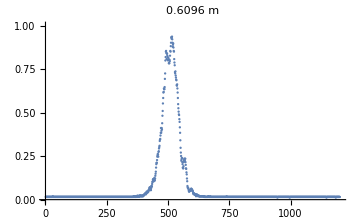

```mathematica
imdMax=Map[Max,imdRaw,{2}];imdMax//Dimensions
Table[ListPlot[imdMax[[i]],ImageSize->Medium,PlotRange->{0,1},PlotLabel->ToString[waistDist[[i]]]<>" m"],{i,1,numImages}]
```

## Process Images

```mathematica
nGauss=30;(*gaussian kernel, i.e. 2σ*)
window={500,500};(*range of pixels to take in*)
```

## Gaussian Fit from Center

```mathematica
AbsoluteTiming[
imdGauss=ParallelMap[GaussianFilter[#,nGauss]&,imdRaw];
center=ParallelMap[Reverse[Position[#,Max[#]][[1]]]&,imdGauss];
]
```

{2.45857,Null}

```mathematica
{x1,x2}=Transpose[Clip[{#-window[[1]],#+window[[1]]},{1,imgDim[[1]]}]&/@center[[;;,1]]];
{y1,y2}=Transpose[Clip[{#-window[[2]],#+window[[2]]},{1,imgDim[[2]]}]&/@center[[;;,2]]];
```

```mathematica
imdProcessed=Table[imdRaw[[i,y1[[i]];;y2[[i]],x1[[i]];;x2[[i]]]],{i,numImages}];
```

## Compare With/Without Gaussian Filter

```mathematica
AbsoluteTiming[imdProcessedGauss=ParallelMap[GaussianFilter[#,nGauss]&,imdProcessed];]
```

{0.576665,Null}

```mathematica
(*Image[#/Max[#]]&/@imdProcessed
Image[#/Max[#]]&/@imdProcessedGauss*)
```

## Fit Images

## Fit Setup

```mathematica
(*sum along axes*)
trans=Transpose[#]&/@imdProcessed;
xList=Total[#]&/@imdProcessed;
yList=Total[#]&/@trans;
```

```mathematica
th1=Table[{imdGauss[[i,center[[i,2]],;;]],imdGauss[[i,;;,center[[i,1]]]]},{i,1,Length[imdGauss]}];
xList=th1[[;;,1]];yList=th1[[;;,2]];
```

```mathematica
(*fitting constraints*)
(*note - adding constraints may hurt fitting*)
xFitConstr={};
yFitConstr={};
```

```mathematica
(*factor of 2 in exponent is b/c intensity is square of electric field*)
xFitEqn={a(Exp[-2((x-x0)/wx)^2])+b};
yFitEqn={a(Exp[-2((y-y0)/wy)^2])+b};
```

## Fitting

```mathematica
(*fitting parameters*)
(*xFitVars=Table[{{x0,Min[{center[[i,1]],500}]},{wx,300},{a,Max[xList[[i]]]},{b,Min[xList[[i]]]}},{i,1,numImages}];
yFitVars=Table[{{y0,Min[{500,center[[i,2]]}]},{wy,150},{a,Max[yList[[i]]]},{b,Min[yList[[i]]]}},{i,1,numImages}];*)
xFitVars=Table[{{x0,center[[i,1]]},{wx,300},{a,Max[xList[[i]]]},{b,Min[xList[[i]]]}},{i,1,numImages}];
yFitVars=Table[{{y0,center[[i,2]]},{wy,150},{a,Max[yList[[i]]]},{b,Min[yList[[i]]]}},{i,1,numImages}];
```

```mathematica
(*fit!*)
AbsoluteTiming[
xFit=ParallelTable[NonlinearModelFit[xList[[i]],Join[xFitEqn,xFitConstr],xFitVars[[i]],x,MaxIterations->1*^6],{i,1,numImages}];
yFit=ParallelTable[NonlinearModelFit[yList[[i]],Join[yFitEqn,yFitConstr],yFitVars[[i]],y,MaxIterations->1*^6],{i,1,numImages}];
]
```

{0.049352,Null}

```mathematica
xFitParams=#["ParameterTable"]&/@xFit
yFitParams=#["ParameterTable"]&/@yFit
```

{ | Estimate | Standard Error | t-Statistic | P-Value
x0 | 909.164 | 0.477439 | 1904.25 | 0.
wx | 165.397 | 1.0134 | 163.21 | 0.
a | 0.581502 | 0.00296796 | 195.926 | 0.
b | 0.0087088 | 0.000843752 | 10.3215 | 3.19181×10^-24, | Estimate | Standard Error | t-Statistic | P-Value
x0 | 1261.52 | 0.54923 | 2296.89 | 0.
wx | 161.138 | 1.16341 | 138.505 | 0.
a | 0.584851 | 0.00352223 | 166.046 | 0.
b | 0.00671004 | 0.000984178 | 6.81791 | 1.30592×10^-11, | Estimate | Standard Error | t-Statistic | P-Value
x0 | 839.401 | 0.500925 | 1675.7 | 0.
wx | 137.071 | 1.04995 | 130.551 | 0.
a | 0.767356 | 0.00493614 | 155.457 | 0.
b | 0.00649551 | 0.00124351 | 5.22351 | 1.98673×10^-7, | Estimate | Standard Error | t-Statistic | P-Value
x0 | 1025.11 | 0.52556 | 1950.51 | 0.
wx | 121.458 | 1.09452 | 110.969 | 0.
a | 0.813411 | 0.00618133 | 131.592 | 0.
b | 0.00775653 | 0.0014451 | 5.36748 | 9.15942×10^-8, | Estimate | Standard Error | t-Statistic | P-Value
x0 | 728.423 | 0.480565 | 1515.76 | 0.
wx | 82.959 | 0.98641 | 84.1019 | 0.
a | 0.421923 | 0.00427077 | 98.7931 | 0.
b | 0.00986574 | 0.000797976 | 12.3635 | 1.34741×10^-33, | Estimate | Standard Error | t-Statistic | P-Value
x0 | 679.473 | 0.34872 | 1948.48 | 0.
wx | 72.3127 | 0.713138 | 101.401 | 0.
a | 0.505449 | 0.00425374 | 118.825 | 0.
b | 0.0095379 | 0.000735483 | 12.9682 | 1.22544×10^-36, | Estimate | Standard Error | t-Statistic | P-Value
x0 | 1020.9 | 0.199542 | 5116.24 | 0.
wx | 65.3219 | 0.407102 | 160.456 | 0.
a | 0.571447 | 0.00304389 | 187.736 | 0.
b | 0.0085708 | 0.000497345 | 17.2331 | 3.62057×10^-61, | Estimate | Standard Error | t-Statistic | P-Value
x0 | 559.644 | 0.0719706 | 7776.02 | 0.
wx | 59.8361 | 0.146566 | 408.254 | 0.
a | 0.632728 | 0.00132622 | 477.09 | 0.
b | 0.00817451 | 0.000206471 | 39.5916 | 2.18491×10^-239, | Estimate | Standard Error | t-Statistic | P-Value
x0 | 1312.27 | 0.0515084 | 25476.8 | 0.
wx | 56.0275 | 0.104765 | 534.795 | 0.
a | 0.357966 | 0.000573247 | 624.453 | 0.
b | 0.00841257 | 0.0000860927 | 97.7152 | 0.}

{ | Estimate | Standard Error | t-Statistic | P-Value
y0 | 466.315 | 0.0864618 | 5393.31 | 0.
wy | 75.5985 | 0.178628 | 423.218 | 0.
a | 0.622391 | 0.00124663 | 499.261 | 0.
b | 0.00907433 | 0.000260696 | 34.8081 | 6.41379×10^-184, | Estimate | Standard Error | t-Statistic | P-Value
y0 | 466.137 | 0.0833687 | 5591.27 | 0.
wy | 75.5937 | 0.172237 | 438.893 | 0.
a | 0.628731 | 0.00121435 | 517.752 | 0.
b | 0.00820384 | 0.000253936 | 32.3067 | 3.9399×10^-165, | Estimate | Standard Error | t-Statistic | P-Value
y0 | 499.964 | 0.0406779 | 12290.8 | 0.
wy | 75.2779 | 0.0840262 | 895.887 | 0.
a | 0.813566 | 0.000769876 | 1056.75 | 0.
b | 0.00811134 | 0.000160596 | 50.5077 | 7.32725×10^-299, | Estimate | Standard Error | t-Statistic | P-Value
y0 | 503.067 | 0.0947241 | 5310.86 | 0.
wy | 78.5632 | 0.195989 | 400.855 | 0.
a | 0.902126 | 0.00190588 | 473.339 | 0.
b | 0.00749123 | 0.0004077 | 18.3744 | 1.30283×10^-66, | Estimate | Standard Error | t-Statistic | P-Value
y0 | 505.371 | 0.0131927 | 38306.9 | 0.
wy | 66.1009 | 0.0271294 | 2436.51 | 0.
a | 0.516492 | 0.000180239 | 2865.59 | 0.
b | 0.00918481 | 0.0000348638 | 263.448 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 506.289 | 0.0191083 | 26495.8 | 0.
wy | 66.6141 | 0.0393039 | 1694.85 | 0.
a | 0.582959 | 0.00029241 | 1993.64 | 0.
b | 0.00944082 | 0.0000568131 | 166.173 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 493.898 | 0.0332817 | 14839.9 | 0.
wy | 66.971 | 0.068469 | 978.122 | 0.
a | 0.617348 | 0.000536504 | 1150.69 | 0.
b | 0.00944585 | 0.00010456 | 90.339 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 509.331 | 0.0236127 | 21570.2 | 0.
wy | 65.4044 | 0.048541 | 1347.41 | 0.
a | 0.645817 | 0.000407624 | 1584.34 | 0.
b | 0.0100166 | 0.0000783687 | 127.814 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 905.18 | 0.0185338 | 48839.3 | 0.
wy | 84.1806 | 0.038458 | 2188.9 | 0.
a | 0.361137 | 0.000139459 | 2589.55 | 0.
b | 0.00829525 | 0.000031085 | 266.857 | 0.}

```mathematica
{x0Fit,wxFit,axFit,bxFit}=Transpose[#[[1,1,2;; ,2]]&/@xFitParams];
{y0Fit,wyFit,ayFit,byFit}=Transpose[#[[1,1,2;; ,2]]&/@yFitParams];
```

## Show

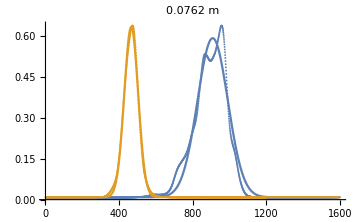
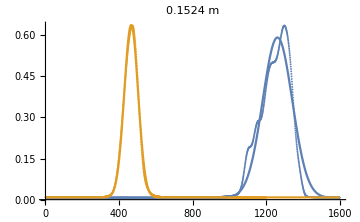
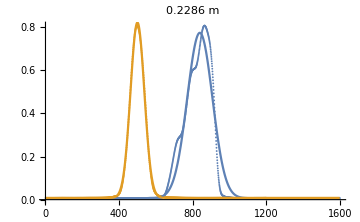
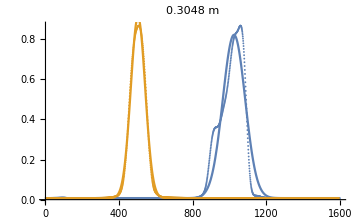
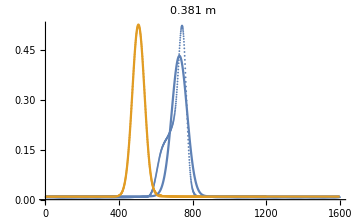
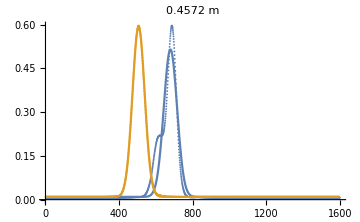
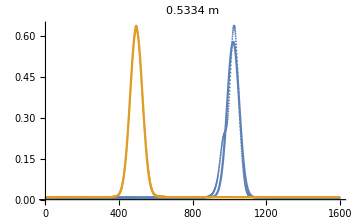
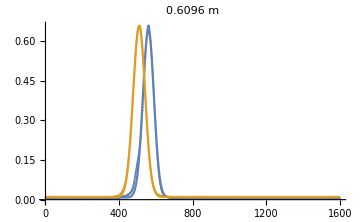

```mathematica
Table[Show[
ListPlot[{xList[[i]],yList[[i]]},ImageSize->Medium,PlotLabel->ToString[waistDist[[i]]]<>" m"],
(*Plot[{xFit[[i]][x],yFit[[i]][x]},{x,0,2 *window[[1]]+1}]*)
Plot[{xFit[[i]][x],yFit[[i]][x]},{x,0,1600}]
],{i,1,numImages}]
```

## Outputs

## Get Points

```mathematica
pos=Table[{x1[[i]]+x0Fit[[i]],y1[[i]]+y0Fit[[i]]},{i,numImages}];
pos=(#/.{x_,y_}->{x,imgDim[[2]]-y})&/@pos;
```

```mathematica
wxFitm=pixelWidth*wxFit;waistX=Transpose[{waistDist,Abs[wxFitm]}];
wyFitm=pixelWidth*wyFit;waistY=Transpose[{waistDist,Abs[wyFitm]}];
```

### Print Results

```mathematica
"w_x="<>ToString[#]<>"μm"&/@(10^6 wxFitm)
"w_y="<>ToString[#]<>"μm"&/@(10^6 wyFitm)
```

{w_x=727.749μm,w_x=709.007μm,w_x=603.112μm,w_x=534.417μm,w_x=365.019μm,w_x=318.176μm,w_x=287.416μm,w_x=263.279μm,w_x=246.521μm}

{w_y=332.633μm,w_y=332.612μm,w_y=331.223μm,w_y=345.678μm,w_y=290.844μm,w_y=293.102μm,w_y=294.673μm,w_y=287.779μm,w_y=370.395μm}

## Get Errors

```mathematica
wxFitErr=#[[1,1,2;;,3]]&/@xFitParams;wxFitErr=wxFitErr[[;;,2]]*pixelWidth;
wyFitErr=#[[1,1,2;;,3]]&/@yFitParams;wyFitErr=wyFitErr[[;;,2]]*pixelWidth;
```

```mathematica
waistXError=Transpose[{waistDist,Abs[wxFitm[[#]]]±wxFitErr[[#]]&/@Range[numImages]}];
waistYError=Transpose[{waistDist,Abs[wyFitm[[#]]]±wyFitErr[[#]]&/@Range[numImages]}];
```

```mathematica
waistXError
waistYError
```

{{0.0762,0.000727749±4.45897×10^-6},{0.1524,0.000709007±5.11901×10^-6},{0.2286,0.000603112±4.61976×10^-6},{0.3048,0.000534417±4.81589×10^-6},{0.381,0.000365019±4.34021×10^-6},{0.4572,0.000318176±3.13781×10^-6},{0.5334,0.000287416±1.79125×10^-6},{0.6096,0.000263279±6.4489×10^-7},{0.9144,0.000246521±4.60964×10^-7}}

{{0.0762,0.000332633±7.85963×10^-7},{0.1524,0.000332612±7.57844×10^-7},{0.2286,0.000331223±3.69715×10^-7},{0.3048,0.000345678±8.62353×10^-7},{0.381,0.000290844±1.19369×10^-7},{0.4572,0.000293102±1.72937×10^-7},{0.5334,0.000294673±3.01264×10^-7},{0.6096,0.000287779±2.1358×10^-7},{0.9144,0.000370395±1.69215×10^-7}}

## Plot w/Error Bars

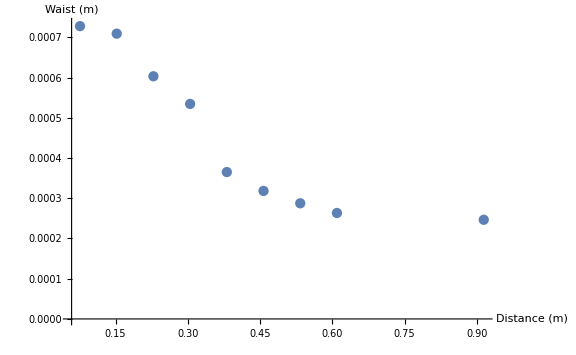
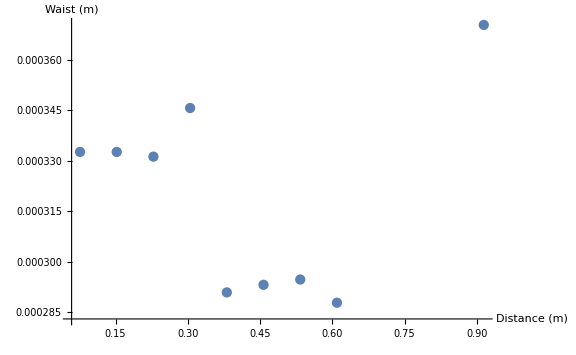

```mathematica
ListPlot[#,ImageSize->Large,PlotRange->Full,AxesLabel->{"Distance (m)","Waist (m)"}]&/@{waistXError,waistYError}
```

## Fit Beam Waist

## Setup

```mathematica
(*note - adding constraints may hurt fitting*)
waistXFitConstr={};
waistYFitConstr={};
```

```mathematica
waistXFitEqn=w0*√(1+((x-x0)/((π*w0^2)/λ0))^2);
waistYFitEqn=w0*√(1+((y-y0)/((π*w0^2)/λ0))^2);
```

```mathematica
waistXFitVars={{w0,Min[waistX[[;;,2]]]},{x0,0}};
waistYFitVars={{w0,Min[waistY[[;;,2]]]},{y0,0}};
```

## Fit

```mathematica
AbsoluteTiming[
waistXFit=NonlinearModelFit[waistX,Join[{waistXFitEqn},waistXFitConstr],waistXFitVars,x,MaxIterations->1*^5,ConfidenceLevel->0.99];
waistYFit=NonlinearModelFit[waistY,Join[{waistYFitEqn},waistYFitConstr],waistYFitVars,y,ConfidenceLevel->0.99];
]
```

{0.003112,Null}

```mathematica
{waistXFitParams,waistYFitParams}={waistXFit["ParameterTable"],waistYFit["ParameterTable"]};
{w0xFit,z0xFit}=Transpose[waistXFitParams[[1,1,2;; ,2]]];
{w0yFit,z0yFit}=Transpose[waistYFitParams[[1,1,2;; ,2]]];
```

## Show

```mathematica
{waistXFitParams,waistYFitParams}
```

{ | Estimate | Standard Error | t-Statistic | P-Value
w0 | 0.000238338 | 0.0000198369 | 12.0149 | 6.30567×10^-6
x0 | 0.702368 | 0.0293111 | 23.9625 | 5.60635×10^-8, | Estimate | Standard Error | t-Statistic | P-Value
w0 | 0.0003035 | 0.0000390159 | 7.77888 | 0.000108965
y0 | 0.446736 | 0.0591155 | 7.557 | 0.000130894}

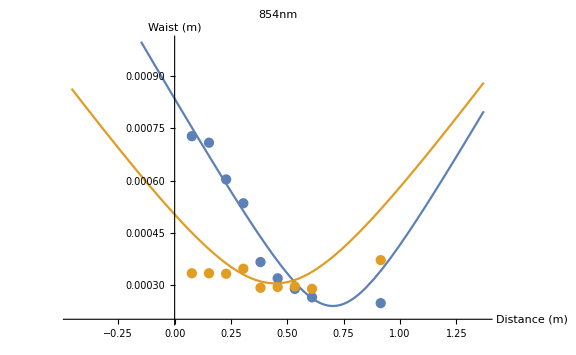

```mathematica
Show[
Plot[{waistXFit[x],waistYFit[x]},{x,-0.5*Max[waistDist],1.5*Max[waistDist]},PlotLabel->ToString[λ0/nm]<>"nm",AxesLabel->{"Distance (m)","Waist (m)"},PlotRange->{0.2mm,1mm}],
ListPlot[{waistX,waistY},PlotRange->Full]
]
```

```mathematica
Solve[waistXFit[x]==waistYFit[x],x]
```

{{x→0.526198},{x→1.7011}}